## High Occupancy Data:

```mathematica
R100D00B00=Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R100D00B00.txt","Data"][[2;;]];
R8DE3B01 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8DE-3B0.1.txt","Data"][[2;;]];
R8DE6B01C1E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B01C1e3.txt","Data"][[2;;]];
R8DE6B01C1E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B01C1e4.txt","Data"][[2;;]];
R8DE6B01C2E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B01C2e4.txt","Data"][[2;;]];
R8DE6B01C5E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B01C5e4.txt","Data"][[2;;]];
R8DE6B02C1E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B02C1e4.txt","Data"][[2;;]];
R8DE6B005C1E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B005C1e4.txt","Data"][[2;;]];
R8DE6B05C1E4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-6B05C1e4.txt","Data"][[2;;]];
R8DE7B005C1E4 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8De-7B005C1e4.txt","Data"][[2;;]];
R50DE6B005C1E4 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R50De-6B005C1e4.txt","Data"][[2;;]];
```

```mathematica
nlmR100D00B00 = NonlinearModelFit[R100D00B00,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE3B01 = NonlinearModelFit[R8DE3B01,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B01CE3 = NonlinearModelFit[R8DE6B01CE3,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B01CE4 = NonlinearModelFit[R8DE6B01CE4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B01C2E4 = NonlinearModelFit[R8DE6B01C2E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B01C5E4 = NonlinearModelFit[R8DE6B01C5E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B02C1E4 = NonlinearModelFit[R8DE6B02C1E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE6B05C1E4 = NonlinearModelFit[R8DE6B05C1E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR8DE7B005C1E4 = NonlinearModelFit[R8DE7B005C1E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
nlmR50DE6B005C1E4 = NonlinearModelFit[R50DE6B005C1E4,A + B Sin[ k ϕ + θ],{A,B,k,θ},ϕ];
```

```mathematica
nlmR100D00B00["ParameterTable"]nlmR8DE3B01["ParameterTable"]nlmR8DE6B01CE3["ParameterTable"]nlmR8DE6B01CE4["ParameterTable"]nlmR8DE6B01C2E4["ParameterTable"]nlmR8DE6B01C5E4["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | -0.0726853 | 0.00392955 | -18.4971 | 3.23097×10^-43
B | -0.32088 | 0.00444563 | -72.1788 | 3.21725×10^-133
k | 1.03649 | 0.025305 | 40.9597 | 3.17957×10^-92
θ | 1.37737 | 0.0392454 | 35.0962 | 1.20252×10^-81  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.0687146 | 0.00203984 | -33.6862 | 6.66736×10^-79
B | -0.32668 | 0.00232891 | -140.271 | 2.32922×10^-183
k | 1.02025 | 0.0125062 | 81.5794 | 2.34434×10^-142
θ | 1.38585 | 0.0191353 | 72.4237 | 1.80141×10^-133  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.0684222 | 0.00288628 | -23.706 | 8.09071×10^-57
B | -0.323064 | 0.00322515 | -100.17 | 8.39263×10^-158
k | 1.03042 | 0.0177586 | 58.0238 | 4.04001×10^-117
θ | 1.36171 | 0.0270563 | 50.3288 | 8.31409×10^-107  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.0674375 | 0.00288144 | -23.4041 | 4.53146×10^-56
B | -0.327485 | 0.00329887 | -99.272 | 4.0202×10^-157
k | 1.016 | 0.0174918 | 58.0842 | 3.39115×10^-117
θ | 1.38951 | 0.0266682 | 52.1035 | 2.65127×10^-109  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.065784 | 0.00150634 | -43.6713 | 1.03801×10^-96
B | -0.328361 | 0.00172668 | -190.169 | 1.34462×10^-206
k | 1.00999 | 0.00898028 | 112.467 | 1.44674×10^-166
θ | 1.39094 | 0.0136048 | 102.239 | 2.39492×10^-159  | Estimate | Standard Error | t-Statistic | P-Value
A | -0.0457538 | 0.0133665 | -3.42303 | 0.000769346
B | -0.309433 | 0.0130194 | -23.767 | 5.72079×10^-57
k | 1.08977 | 0.0775262 | 14.0568 | 1.25777×10^-30
θ | 1.18232 | 0.112461 | 10.5131 | 2.15746×10^-20

## Low Occupancy Data (λ = 0.05):

#### Change Dark Rate:

```mathematica
DE3L005 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8DE-3B005C1e5L005.txt","Data"][[2;;]];
DE6 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8DE-6B005C1e5L01.txt","Data"][[2;;]];
DE7 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8DE-7B005C1e5L01.txt","Data"][[2;;]];
DE5 =Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8De-5B005C1e5L01.txt","Data"][[2;;]];
DE72 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\R8DE-7B005C1e5L01.txt","Data"][[2;;]];
DE4 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8De-4B005C1e5L01.txt","Data"][[2;;]];
DE3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8De-3B005C1e5L01.txt","Data"][[2;;]];
DE2 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8De-2B005C1e5L01.txt","Data"][[2;;]];
D2E2 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8D2e-2B005C1e5L01.txt","Data"][[2;;]];
D5E3 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Dark Count\\R8D5e-3B005C1e5L01.txt","Data"][[2;;]];
```

```mathematica
nlmD2E2= NonlinearModelFit[D2E2,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE2 = NonlinearModelFit[DE2,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmD5E3= NonlinearModelFit[D5E3,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
(*nlmDE3L005 = NonlinearModelFit[DE3L005,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];*)
nlmDE3 = NonlinearModelFit[DE3,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE4 = NonlinearModelFit[DE4,Centre+Amplitude Sin[Frequency ϕ+Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE5 = NonlinearModelFit[DE5,Centre+Amplitude Sin[Frequency ϕ+Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE6 = NonlinearModelFit[DE6,Centre+Amplitude Sin[Frequency ϕ+Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE7 = NonlinearModelFit[DE7,Centre +Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
nlmDE72 = NonlinearModelFit[DE72,Centre+Amplitude Sin[Frequency ϕ + Phase],{Centre,Amplitude,Frequency,Phase},ϕ];
```

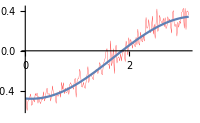
D = 2×10^-2 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | -0.0677332 | 0.0124323 | -5.44816 | 1.6849×10^-7
Amplitude | -0.412933 | 0.0152001 | -27.1664 | 4.81755×10^-65
Frequency | 0.993312 | 0.0623444 | 15.9327 | 4.99303×10^-36
Phase | 1.45914 | 0.097129 | 15.0227 | 2.03151×10^-33

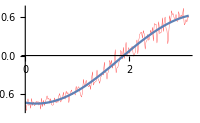
D = 10^-2 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | -0.0506676 | 0.0210715 | -2.40455 | 0.0172238
Amplitude | -0.705899 | 0.0233466 | -30.2356 | 8.06524×10^-72
Frequency | 0.977777 | 0.0499966 | 19.5569 | 4.22752×10^-46
Phase | 1.36291 | 0.0713052 | 19.1138 | 6.68069×10^-45

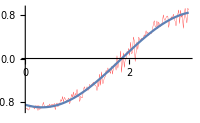
D = 5×10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | -0.016277 | 0.0184014 | -0.884554 | 0.377597
Amplitude | -0.88003 | 0.0185771 | -47.3717 | 1.79699×10^-102
Frequency | 1.03547 | 0.0345512 | 29.9693 | 2.99348×10^-71
Phase | 1.23971 | 0.0486892 | 25.4617 | 4.5142×10^-61

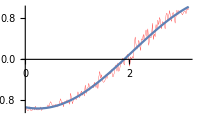
D = 10^-3 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.131385 | 0.0383033 | 3.43011 | 0.000750773
Amplitude | -1.09161 | 0.0404651 | -26.9766 | 1.31021×10^-64
Frequency | 0.875004 | 0.0391258 | 22.3639 | 1.87396×10^-53
Phase | 1.35787 | 0.0477838 | 28.4169 | 7.32924×10^-68

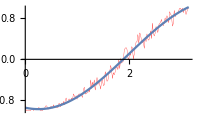
D = 10^-4 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.0929922 | 0.0307552 | 3.02363 | 0.00286893
Amplitude | -1.06597 | 0.0324884 | -32.8108 | 3.71574×10^-77
Frequency | 0.910436 | 0.0357582 | 25.4609 | 4.53434×10^-61
Phase | 1.33943 | 0.0454983 | 29.4392 | 4.16963×10^-70

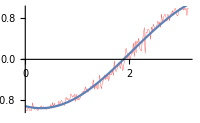
D = 10^-5 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.153735 | 0.0381198 | 4.03295 | 0.0000817801
Amplitude | -1.10773 | 0.0390987 | -28.3315 | 1.13478×10^-67
Frequency | 0.900004 | 0.0384262 | 23.4216 | 4.09933×10^-56
Phase | 1.30185 | 0.0467607 | 27.8406 | 1.42458×10^-66

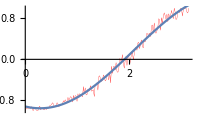
D = 10^-6 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.157462 | 0.0382044 | 4.12157 | 0.0000577388
Amplitude | -1.11379 | 0.0394105 | -28.2613 | 1.62722×10^-67
Frequency | 0.881513 | 0.0367427 | 23.9916 | 1.60244×10^-57
Phase | 1.31905 | 0.0440045 | 29.9754 | 2.90522×10^-71

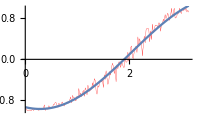
D = 10^-7 -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.126345 | 0.0370528 | 3.40987 | 0.000805011
Amplitude | -1.09601 | 0.038338 | -28.5882 | 3.05736×10^-68
Frequency | 0.899269 | 0.0385289 | 23.3401 | 6.53839×10^-56
Phase | 1.31578 | 0.0473277 | 27.8014 | 1.74538×10^-66

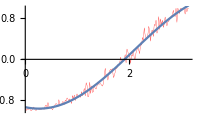
D = 10^-7(2) -Graphics-  | Estimate | Standard Error | t-Statistic | P-Value
Centre | 0.157533 | 0.0408669 | 3.85479 | 0.000161897
Amplitude | -1.12067 | 0.0426512 | -26.2751 | 5.49907×10^-63
Frequency | 0.867946 | 0.0386502 | 22.4565 | 1.08993×10^-53
Phase | 1.34398 | 0.0461684 | 29.1103 | 2.17136×10^-69

```mathematica
"D = 2×10^-2" nlmD2E2["ParameterTable"]Show[ListLinePlot[D2E2,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmD2E2],{ϕ,0,π}]]
"D = 10^-2" nlmDE2["ParameterTable"]Show[ListLinePlot[DE2,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE2],{ϕ,0,π}]]
(*"D = 10^-3" nlmDE3L005["ParameterTable"]Show[ListLinePlot[DE3L005,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE3L005],{ϕ,0,π}]]
*)
"D = 5×10^-3" nlmD5E3["ParameterTable"]Show[ListLinePlot[D5E3,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmD5E3],{ϕ,0,π}]]
"D = 10^-3" nlmDE3["ParameterTable"]Show[ListLinePlot[DE3,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE3],{ϕ,0,π}]]
"D = 10^-4" nlmDE4["ParameterTable"]Show[ListLinePlot[DE4,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE4],{ϕ,0,π}]]
"D = 10^-5" nlmDE5["ParameterTable"]Show[ListLinePlot[DE5,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE5],{ϕ,0,π}]]
"D = 10^-6" nlmDE6["ParameterTable"]Show[ListLinePlot[DE6,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE6],{ϕ,0,π}]]
"D = 10^-7" nlmDE7["ParameterTable"]Show[ListLinePlot[DE7,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE7],{ϕ,0,π}]]
"D = 10^-7(2)" nlmDE72["ParameterTable"]Show[ListLinePlot[DE72,PlotStyle->Directive[Thickness[.001],Red],ImageSize->200],Plot[Normal[nlmDE72],{ϕ,0,π}]]
```

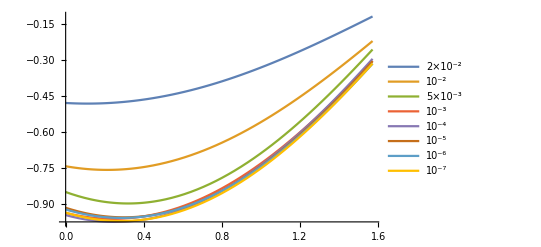

```mathematica
Plot[{Normal[nlmD2E2],Normal[nlmDE2],Normal[nlmD5E3],Normal[nlmDE3],Normal[nlmDE4],Normal[nlmDE5],Normal[nlmDE6],Normal[nlmDE7]},{ϕ,0,π/2},PlotLegends->{"2×10^-2","10^-2","5×10^-3","10^-3","10^-4","10^-5","10^-6","10^-7"}]
```

#### Change Quantum Efficiency:

```mathematica
R10CE5 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R10D00B005C1e5L01.txt","Data"][[2;;]];
R10CE6 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R10D00B005C1e6L01.txt","Data"][[2;;]];
R25CE5 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R25D00B005C1e5L01.txt","Data"][[2;;]];
R50CE5 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R50D00B005C1e5L01.txt","Data"][[2;;]];
R100CE5 = Import["C:\\Users\\tobyh\\Documents\\ANU\\2020\\Semester 2\\SCNC2101\\GITHUB Repositories\\Momentum_Bells_test\\toby\\Low Occupancy Data\\Change Retention\\R100D00B005C1e5L01.txt","Data"][[2;;]];
```

```mathematica
nlmR10CE5 = NonlinearModelFit[R10CE5,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
nlmR10CE6 = NonlinearModelFit[R10CE6,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
nlmR25CE5 = NonlinearModelFit[R25CE5,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
nlmR50CE5 = NonlinearModelFit[R50CE5,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
nlmR100CE5 = NonlinearModelFit[R100CE5,A + B Sin[ϕ+θ],{A,B,k,θ},ϕ];
```

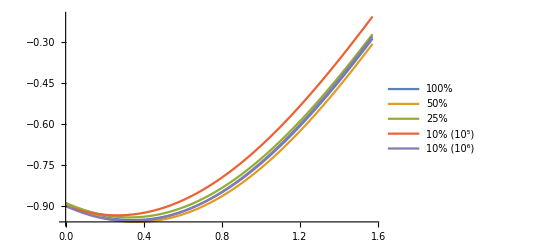

```mathematica
Plot[{Normal[nlmR100CE5],Normal[nlmR50CE5],Normal[nlmR25CE5],Normal[nlmR10CE5],Normal[nlmR10CE6]},{ϕ,0,π/2},PlotLegends->{"100%","50%","25%","10% (10^5)","10% (10^6)"}]
```

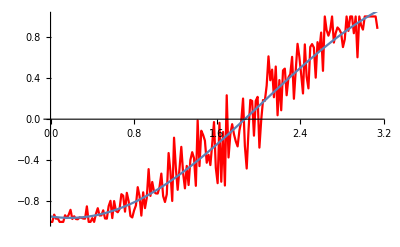

```mathematica
Show[ListLinePlot[R25CE5,PlotStyle->Red],Plot[Normal[nlmR25CE5],{ϕ,0,π}]]
```